Determination of the correction factors from FRET labeled samples using PIE or Alex

Literaturpaclet:Fretica/tutorial/DetermintaionOfTheRCMFromFRETLabledSamplesUsingPIEOrAlex#427957822 | Example with simulated datapaclet:Fretica/tutorial/DetermintaionOfTheRCMFromFRETLabledSamplesUsingPIEOrAlex#369752238
Theory for a 2-channel instrumentpaclet:Fretica/tutorial/DetermintaionOfTheRCMFromFRETLabledSamplesUsingPIEOrAlex#420196562 |

```mathematica
Needs["Fretica`"]
```

Literatur

2005 Lee et al. introduced an elegant method for determining the correction factors from Alex (or PIE) measurements of FRET labeled sample molecules. The method has been later adapted in the multi-laboratory benchmark study (Hellenkamp et al.)

Lee NK, Kapanidis AN, Wang Y, Michalet X, Mukhopadhyay J, Ebright RH, Weiss S.
Accurate FRET measurements within single diffusing biomolecules using alternating-laser excitation. Biophys J. 2005;88(4):2939-2953. https://doi.org/10.1529/biophysj.104.054114

Hellenkamp, B., Schmid, S., Doroshenko, O. et al. Precision and accuracy of single-molecule FRET measurements—a multi-laboratory benchmark study. Nat Methods 15, 669–676 (2018). https://doi.org/10.1038/s41592-018-0085-0

### Definitions

```mathematica
cfunc[color_] := (If[# == 0., RGBColor[1, 0, 0, 0], Lighter[color, 1 - #]] &)
```

```mathematica
gaussian2D[x0:{_,_},σ:{_,_},α_,A_][x:{_,_}]:=Module[{rot,B},
rot=RotationMatrix[α];
B=DiagonalMatrix[1/(2 σ^2)];
Abs[A] Exp[-{rot.(x-x0)}.B.(rot.(x-x0))][[1]]
]
```

```mathematica
GetEllipsoid[x0:{_,_},σ:{_,_},α_]:=Module[{rot,B,elipsoid},
rot=RotationMatrix[α];
B=DiagonalMatrix[σ^2];
elipsoid=Ellipsoid[x0,rotᵀ.B.rot]
]
```

```mathematica
makemodelG2D[symbols_List]:=
{
Total@Table[gaussian2D[{x01[i],x02[i]},{σx1[i],σx2[i]},α[i],A[i]][{x1,x2}],{i,symbols}],Flatten@Table[{x01[i],x02[i],σx1[i],σx2[i],α[i],A[i]},{i,symbols}]
}
```

#### EvsS

```mathematica
EvsS[γ_,β_,d_,b_][{nda_,ndd_, naa_}]:=Module[{DA,Dtot},
DA=nda-(ndd *β  )-(naa*d);
Dtot=(DA+γ ndd);
{DA/Dtot,Dtot/(Dtot+naa /b)}ᵀ
]
```

```mathematica
EvsSPlot[data_,o___]:=Block[{xmin,xmax,ymin,ymax,x,y,mainplot,xhist,yhist,opts=Flatten[{o}]},
mainplot=DensityHistogram[data,{-0.25,1.25,1/80},FilterRules[opts,Options[ListPlot]],Frame->True,Axes->False,AspectRatio->1,PlotRange->All,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];

mainplot]
```

#### 2D Gaussian

```mathematica
gaussian2D[x0:{_,_},σ:{_,_},α_,A_][x:{_,_}]:=Module[{rot,B},
rot=RotationMatrix[α];
B=DiagonalMatrix[1/(2 σ^2)];
Abs[A] Exp[-{rot.(x-x0)}.B.(rot.(x-x0))][[1]]
]
```

```mathematica
GetEllipsoid[x0:{_,_},σ:{_,_},α_]:=Module[{rot,B,elipsoid},
rot=RotationMatrix[α];
B=DiagonalMatrix[σ^2];
elipsoid=Ellipsoid[x0,rotᵀ.B.rot]
]
```

```mathematica
makemodelG2D[symbols_List]:=
{
Total@Table[gaussian2D[{x01[i],x02[i]},{σx1[i],σx2[i]},α[i],A[i]][{x1,x2}],{i,symbols}],Flatten@Table[{x01[i],x02[i],σx1[i],σx2[i],α[i],A[i]},{i,symbols}]
}
```

#### EvsS

```mathematica
EvsS[γ_,β_,d_,b_][{nda_,ndd_, naa_}]:=Module[{DA,Dtot},
DA=nda-(ndd *β  )-(naa*d);
Dtot=(DA+γ ndd);
{DA/Dtot,Dtot/(Dtot+naa /b)}ᵀ
]
```

```mathematica
EvsSPlot[data_,o___]:=Block[{xmin,xmax,ymin,ymax,x,y,mainplot,xhist,yhist,opts=Flatten[{o}]},
mainplot=DensityHistogram[data,{-0.25,1.25,1/80},FilterRules[opts,Options[ListPlot]],Frame->True,Axes->False,AspectRatio->1,PlotRange->All,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];

mainplot]
```

#### EvsS fitting

```mathematica
makeESfitModel[elist_List]:=Module[{model,peaksymbols,s,guessD,guessA,guessF},
peaksymbols=Join[{"d","a"},Table["f"<>ToString[i],{i,Length[elist]}]];
model=makemodelG2D[peaksymbols];
guessD={{{x01["d"],0},{x02["d"],1},{σx1["d"],0.1},{σx2["d"],0.1},{α["d"],0.05},{A["d"],10.}}};
guessA={{{x01["a"],0.8},{x02["a"],0},{σx1["a"],0.5},{σx2["a"],0.1},{α["a"],0.05},{A["a"],10.}}};
guessF=Table[(s="f"<>ToString[i];{{x01[s],elist[[i]]},{x02[s],0.5},{σx1[s],0.1},{σx2[s],0.1},{α[s],0.05},{A[s],10.}}),{i,Length[elist]}];
{model[[1]],peaksymbols,Flatten[Join[guessD,guessA,guessF],1]}
]
```

```mathematica
FitESData[{γ_,β_,d_,b_},fretguess_List][{nda_,ndd_, naa_}]:=Module[{data,fitdat,fit,model,psymbols,guess,pl,ellipses,eslist},
data=EvsS[γ,β,d,b][{nda,ndd, naa}];
fitdat=Histo2D[data,{-0.25,1.25,1/30},{-0.25,1.25,1/30},PlotRange->All,FOutput->FData];
{model,psymbols,guess}=makeESfitModel[fretguess];
fit=FindFit[fitdat,model,guess,{x1,x2}];
pl=EvsSPlot[data,FrameLabel->{"E","S"},PlotRange->All];
ellipses=GetEllipsoid@@@Table[{{x01[i],x02[i]},{σx1[i],σx2[i]},α[i]},{i,psymbols}]/.fit;
eslist=Table[{x01[s],x02[s]}/.fit,{s,psymbols}];
{psymbols,eslist,Show[pl,Graphics[{EdgeForm[{Thick,Red}],FaceForm[],ellipses}]],fit}
]
```

#### FDetermineCorrectionFactorsFromPIE

```mathematica
Clear[FDetermineCorrectionFactorsFromPIE];
SetAttributes[FDetermineCorrectionFactorsFromPIE,HoldFirst]
FDetermineCorrectionFactorsFromPIE[output_,{nda_,ndd_, naa_}]:=Module[{whiteLocatorRing,color,thickness,size,radius,lineThickness,opacity,γ,β,d,γpie, beta,gamma,dir,gammapie,ESraw,ESprox,ES,eprox},
{γ,β,d,γpie}={1,0,0,1};
ESraw:=EvsS[1,0,0,1][{nda,ndd, naa}];
ESprox:=EvsS[1,β,d,1][{nda,ndd, naa}];
ES:=EvsS[γ,β,d,1/γpie][{nda,ndd, naa}];

Manipulate[
TabView[{"ct, direct ex"->DynamicModule[{pts={{0,1},{1,0}}},
(*Begins the column with all the content of the manipulate*)Column[{(*Begin LocatorPane*)Row[{Dynamic@LocatorPane[Dynamic[pts],Dynamic@Show[EvsSPlot[ESraw,FrameLabel->{"Eraw","Sraw"}],ImageSize->size],LocatorAutoCreate->True,(*Begin Locator appearance*)Appearance->If[whiteLocatorRing,Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]},{White,AbsoluteThickness[thickness],Circle[{0,0},radius]}},ImageSize->10],Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]}},ImageSize->10]](*End Locator appearance*)]}],(*End LocatorPane*)(*Begin of the block of InputFields*)Row[{Style["D-only E:"],InputField[Dynamic[pts[[1,1]]],FieldSize->7],Spacer[20],Style["A-only S:"],InputField[Dynamic[pts[[2,2]]],FieldSize->7]}],Row[{Style["crosstalk β:"],InputField[Dynamic[pts[[1,1]]/(1-pts[[1,1]])],FieldSize->7],Spacer[20],Style["direct ex. d:"],InputField[Dynamic[Dynamic[ pts[[2,2]]/(1-pts[[2,2]])]],FieldSize->7]}](*End of the block of InputFields*),
Spacer[0],(*Begin button "Make the list of the curve's points"*)Button[Style["Set beta and d",Bold],
β=pts[[1,1]]/(1-pts[[1,1]]);
d= pts[[2,2]]/(1-pts[[2,2]]);

](*End of button "Make the list..."*)},Alignment->Center](*End of column with all the content of the manipulate*)
],"γ, γpie"->DynamicModule[{pts={{0.2,0.5},{0.8,0.5}},x1=Null,x2=Null,y1=Null,y2=Null,X1,X2,Y1,Y2,ΔX,ΔY,g,myRound},myRound[x_]:=Round[1000*x]/1000//N;
(*Begins the column with all the content of the manipulate*)Column[{(*Begin LocatorPane*)Row[{Dynamic@LocatorPane[Dynamic[pts],Dynamic@Show[EvsSPlot[ESprox,FrameLabel->{"Eprox","Sprox"}],ImageSize->size],LocatorAutoCreate->True,(*Begin Locator appearance*)Appearance->If[whiteLocatorRing,Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]},{White,AbsoluteThickness[thickness],Circle[{0,0},radius]}},ImageSize->10],Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]}},ImageSize->10]](*End Locator appearance*)]}],(*End LocatorPane*)(*Begin of the block of InputFields*)Row[{Style["{γ, γpie}="],Dynamic[{gamma,gammapie}/.NonlinearModelFit[pts,1/(1+1/gammapie (eprox+gamma-eprox gamma)),{gammapie,gamma},eprox]["BestFitParameters"]],Spacer[20]}],(*End of the block of InputFields*)(*Begin the buttons row*)Row[{Spacer[15],(*Begin button "Memorize scale X"*)Button["Clear",pts=pts[[1;;2]]],(*End of button "Memorize scale X"*)Spacer[70],(*Begin button "Memorize scale Y"*)Button["Set γ",{γ,γpie}={gamma,gammapie}/.NonlinearModelFit[pts,1/(1+1/gammapie (eprox+gamma-eprox gamma)),{gammapie,gamma},eprox]["BestFitParameters"]](*End of button "Memorize scale Y"*)}],(*End the buttons row*)Spacer[0]},Alignment->Center](*End of column with all the content of the manipulate*)
],
"E vs S"->DynamicModule[{pts={{0.2,0.5},{0.8,0.5}},x1=Null,x2=Null,y1=Null,y2=Null,X1,X2,Y1,Y2,ΔX,ΔY,g,myRound},myRound[x_]:=Round[1000*x]/1000//N;
(*Begins the column with all the content of the manipulate*)Column[{(*Begin LocatorPane*)Row[{Dynamic@LocatorPane[Dynamic[pts],Dynamic@Show[EvsSPlot[ES,FrameLabel->{"E","S"}],ImageSize->size],LocatorAutoCreate->True,(*Begin Locator appearance*)Appearance->If[whiteLocatorRing,Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]},{White,AbsoluteThickness[thickness],Circle[{0,0},radius]}},ImageSize->10],Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]}},ImageSize->10]](*End Locator appearance*)]}],(*End LocatorPane*)(*Begin of the block of InputFields*)(*End the buttons row*)Spacer[0],Row[{Dynamic@pts}],Row[Dynamic@{"γ"->γ,"γpie"->γpie, "d"->d,"β"->β, "α"->d/γpie}],(*Begin button "Make the list of the curve's points"*)Button[Style["Write correction factors to '"<>SymbolName[Unevaluated[output]]<>"'",Bold],output={"γ"->γ,"γpie"->γpie, "d"->d,"β"->β, "α"->d/γpie}](*End of button "Make the list..."*)},Alignment->Center](*End of column with all the content of the manipulate*)
]}
],(*End of the DynamicModule*)
(*The massive of sliders begins*)Column[{Row[{Control[{{whiteLocatorRing,True,"white locator ring"},{True,False}}],Spacer[50]}],Row[{Spacer[32.35],Control[{{size,450,"image size"},300,800}],Spacer[38.5],Control[{{opacity,0.5,"Opacity"},0,1}]}],Row[{Spacer[10.],Control[{{thickness,1,"Circle thickness"},0.5,5}],Spacer[13.65],Control[{{lineThickness,1,"Line thickness"},0,10}]}],Row[{Spacer[22.8],Control[{{color,Red,"Color"},Red}],Spacer[59.3],Control[{{radius,0.5,"Radius"},0,3}]}]},Alignment->Center],(*The massive of sliders ends*)(*Definitions of sliders*)ControlType->{Checkbox,Slider,Slider,Slider,Slider,ColorSlider,Slider},ControlPlacement->Top,SaveDefinitions->True,FrameLabel->{{None,None},{None,Style["Determine correction factors from PIE",Bold]}}
]
];
```

Theory for a 2-channel instrument

In a PIE or Alex measurement of a FRET-labelled sample we obtain for each burst :
nDD : donor photons after donor excitation
nDA : acceptor photons after donor excitation
nAA : acceptor photons after acceptor excitation

We assume here that the counts are only corrected for background photons.
Four correction factors are needed to obtain corrected values for E and S from theses three counts. Different choices are possible. Lee et al. use these four factors:
γ=(Q_A η_A)/(Q_D η_D) (with quantum yields Q_(A,D) and detection efficiencies η_(A,D))

β (crosstalk, leakage)

d=(I_D ϵ_D(λ_A))/(I_A ϵ_A(λ_A))= γ_PIE α/(1-α) (direct excitation )

b= (I_A ϵ_A(λ_A))/(I_D ϵ_D(λ_D))=1/γ_PIE 
Instead of d and b, Fretica uses α and γ_PIE.The relations between these two pairs of correction factors are indicated. Note that α=(ϵ_A(λ_D))/(ϵ_A(λ_D)+ϵ_D(λ_D)) is also defined for measurements without PIE or Alex (I_A=0) . λ_D and λ_A are the wavelengths of the light sources for donor and acceptor excitation, respectively. ϵ_D(λ) and ϵ_A(λ) are the absorption spectra of the donor and acceptor dyes. 
The corrected transfer efficiency E and stoichiometry ration S are  calculated from:

```mathematica
EvsS[γ,β,d,b][{nda,ndd, naa}]
```

{(-d naa+nda-ndd β)/(-d naa+nda-ndd β+ndd γ),(-d naa+nda-ndd β+ndd γ)/(naa/b-d naa+nda-ndd β+ndd γ)}

The correction factors are determined in two steps.

### Step 1: Determination of crosstalk (β) and direct excitation (d)

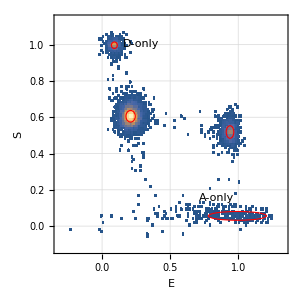
β and d can be obtained from the donor-only and the acceptor-only subpopulations: 

First one  calculates EvsS[1,0,0,1][ {nda ,ndd , naa}] for all bursts.

-Graphics-

Form the mean position in ⟨E⟩_Donly of the donor-only population one calculates:
 β =(⟨E⟩_Donly)/(1-⟨E⟩_Donly)
Form the mean position in ⟨S⟩_Aonly of the acceptor-only population one calculates:
 d =(⟨S⟩_Aonly)/(1-⟨S⟩_Aonly)

### Step 2: Determination of γ and b=1/γ_PIE

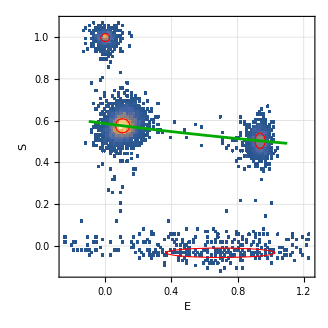
Then one  calculates EvsS[ 1, β, d, 1 ][ {nda ,ndd , naa}] for all bursts and determines the positions of the FRET populations. At least two populations are needed, (They can also be obtained from measurements of different samples.)

These data are fitted with 

Sapp (e) = (1 + b (e + γ - e γ))^-1

for obtaining γ and b

-Graphics-

### Settings in Fretica

The correction factors are finally set in Fretica by calling:

FSetRCM[(1 | -β
0 | γ)]
FSetDirectAcceptorExcitation[ (d b)/(1+d b)]
FSetPIEGamma[1/b]

Here it is assumed that the data were measured with a 2-channel instrument.

Example with simulated data

```mathematica
FOpenTTTR[$FreticaExamples<>"\\Sim05.ht3"]
```

1

Settings

```mathematica
FSetRCM[{{1,0},{0,1}}];
FSetDirectAcceptorExcitation[0];
FEnablePie[True];
FSetFRETRoutes[{"A","D"}];
FSetPIERoutes[FGetAcceptorRoutes[]];
FSetChannelConstraints[chmain={66,1500}];
FSetPIEChannelConstraints[chpie={1500,3000}];
```

Burst identification:

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,50,1000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,1000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
FCutAsymmetricBursts[1];
FSelectBursts[All];
burstcount=FGetBurstListSize[]
```

{879.758,1783.03,0.,0.,0.,0.}

10978

8162

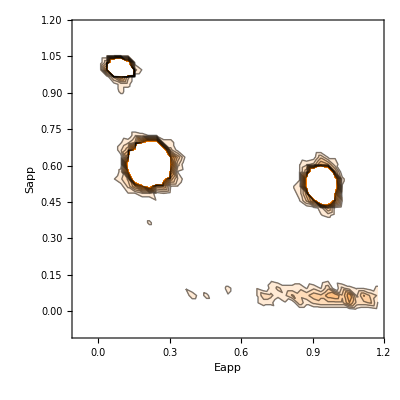

```mathematica
FParamHisto2D["Eapp","Sapp",{-0.1,1.2,.03},{-0.1,1.2,0.03},PlotRange->{0,20},Contours->8,ColorFunction->cfunc[RGBColor[1, 0.5, 0]],AspectRatio->1]
```

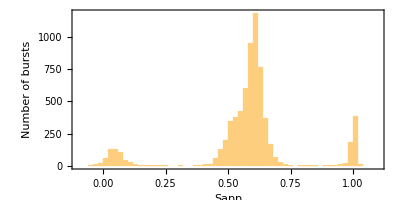

```mathematica
FParamHisto["Sapp",{-0.1,1.1,0.02}]
```

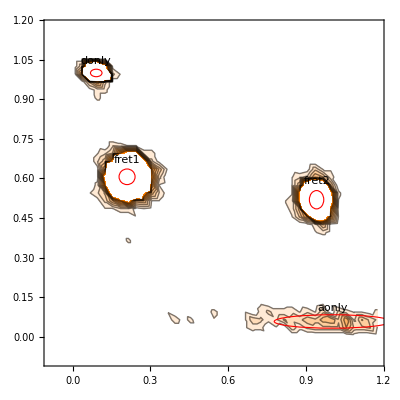

{{0.0911491,0.999664},{0.209947,0.60638},{0.94035,0.51953},{1.00183,0.0584589}}

```mathematica
posguess={{0.07074,1.014},{0.2112,0.6103},{0.9427,0.5252},{1,0.07052}};
fitdata=FParamHisto2D["Eapp","Sapp",{-0.1,1.2,.03},{-0.1,1.2,0.03},FOutput->FData];
fit=FFitPeaks2D[fitdata,{"donly","fret1","fret2","aonly"},posguess,PlotRange->{0,20},Contours->8,ColorFunction->cfunc[RGBColor[1, 0.5, 0]],AspectRatio->1];
fit[[2]]
fit[[1]]
```

```mathematica
edonly=fit[[1]][[1,1]]
esfret=fit[[1]][[2;;3]]
saonly=fit[[1]][[4,2]]
```

0.0911491

{{0.209947,0.60638},{0.94035,0.51953}}

0.0584589

```mathematica
cfactors = FPIECorrectionFactors[edonly, saonly, esfret]
```

{Freticaαβγγpie→{0.0588184,0.100291,0.701862,0.993508},Hellenkampαβγδ→{0.100291,1.00653,0.701862,0.0620885},EvsScorrected→{{0.140187,0.5},{0.954435,0.5}},γfit→FittedModel[1/(1.70645+0.300086 Fretica`Private`e$48588)]}

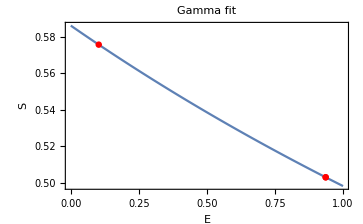

```mathematica
gammafit="γfit"/.cfactors;
Show[Plot[gammafit[e],{e,0,1}],ListPlot[{gammafit["Data"]},PlotStyle->{Red,Orange}],PlotLabel->"Gamma fit",FrameLabel->{"E","S"},PlotRange->All,Frame->True,Axes ->False]
```

```mathematica
FSetFretCorrectionFactors["Freticaαβγγpie"/.cfactors,G=1];
FGetRCM[]//MatrixForm
FFindBurstsDeltaT[0.00015,50,1000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
FCutAsymmetricBursts[1];
```

(1. | -0.100291 | 0. | 0. | 0. | 0.
0. | 0.701862 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

9429

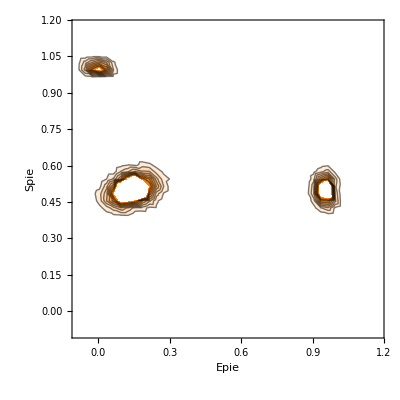

```mathematica
FParamHisto2D["Epie","Spie",{-0.1,1.2,.03},{-0.1,1.2,0.03},PlotRange->{0,100},Contours->8,ColorFunction->cfunc[RGBColor[1, 0.5, 0]],AspectRatio->1]
```

```mathematica
posguess=posguess={{0,1},{0.2112,0.5},{0.9427,0.5}};
fitdata=FParamHisto2D["Epie","Spie",{-0.1,1.2,.03},{-0.1,1.2,0.03},FOutput->FData];
fit=FFitPeaks2D[fitdata,{"donly","fret1","fret2"},posguess,PlotRange->{0,300},Contours->8,ColorFunction->cfunc[RGBColor[1, 0.5, 0]],AspectRatio->1];
fit[[2]]
fit[[1]]
```

-Graphics-

{{0.000539248,1.00392},{0.141705,0.501164},{0.954302,0.499265}}

| Related Guides
▪Fretica

| Related Tech Notes
▪Correction factors, route correction matrix (RCM), transfer efficiencies
▪Determination of the RCM from dye solutions